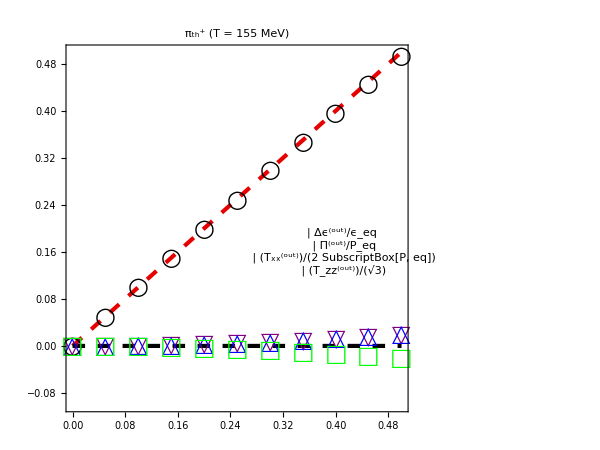

```mathematica
(*PION GAS*)

T0 = 0.155;
mass = 0.140;
sign = -1;
frac=Table[0.05*i,{i,0,10}];

Δϵoverϵdata = {0.0,0.000177438930089258,0.000709840303830367,0.00159745803323386,0.00284071584403067,0.0044402080754804,0.00639670078131083,0.008711133113108,0.0113846189565445,0.0144184487813708,0.0178140916520186};

ΠoverPdata = {0.0,0.000198695354897897,0.000794903501501491,0.0017889912587842,0.00318157190966066,0.004973508098456,0.00716591592914137,0.00976017030609974,0.0127579115715504,0.0161610535058063,0.0199717927687541};

a1overPdata = {0.0,0.0499930404020064,0.0999443092836873,0.149811965368435,0.199554027555123,0.249128304228996,0.298492321649638,0.347603251125433,0.396417834702294,0.444892309121805,0.492982327846549};

a2overPdata = {0.0,-0.000202975948484678,-0.000812177613730019,-0.00182842808066127,-0.00325310458806561,-0.00508814671754897,-0.00733606794291235,-0.0099999706231503,-0.0130835645415811,-0.016591189110486,-0.0205278393714698};

style={Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]]};

label=Panel[Grid[{{Graphics[{EdgeForm[Directive[Thick,Purple]],White,Polygon[{{1,Sqrt[3]},{0,0},{-1,Sqrt[3]}}]},ImageSize->16],Style["Δϵ^(out)/ϵ_eq",FontSize->14]},{Graphics[{EdgeForm[Directive[Thick,Blue]],White,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]},ImageSize->16],Style["Π^(out)/P_eq",FontSize->14]},
{Graphics[{Directive[Thick,Black],Circle[]},ImageSize->16],Style["T_xx^(out)/(2 SubscriptBox[P, eq])",FontSize->18]},{Graphics[{EdgeForm[Directive[Thick,Green]],White,Rectangle[]},ImageSize->16],Style["T_zz^(out)/(√3)",FontSize->18]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΠoverPplot = Table[{frac[[i]],ΠoverPdata[[i]]},{i,1,Length[frac]}];
a1overPplot = Table[{frac[[i]],a1overPdata[[i]]},{i,1,Length[frac]}];
a2overPplot = Table[{frac[[i]],a2overPdata[[i]]},{i,1,Length[frac]}];

Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.1,0.5},ImageSize->600,PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->22},AspectRatio->0.75],
ListPlot[{Δϵoverϵplot,ΠoverPplot,a1overPplot ,a2overPplot },PlotRange->{-0.1,0.5},ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{▽,24},{△,24},{○,24},{□,24}},PlotStyle->{Purple,Blue,Black,Green},BaseStyle->{FontSize->22},AspectRatio->0.75]}
},Epilog->Inset[label,{0.41,0.16}],ImageSize->{600,500},FrameLabel->{"T_xx^(in)/(2 SubscriptBox[P, eq])"},PlotLabel->Style["π_th^+ (T = 155 MeV)",FontSize->24]]
```